## Développement limité de la fonction logarithme népérien

#### Formulation de la fonction log() à partir de la fonction arc-tangente hyperbolique

```mathematica
FullSimplify[2ArcTanh[(x-1)/(x+1)],x>0]
```

Log[x]

#### Développement en série de la fonction tanh^-1()

```mathematica
Series[ArcTanh[x],{x,0,7}]
```

x+x^3/3+x^5/5+x^7/7+O[x]^8

#### Développement limité à l’ordre n et vérification de l’identité avec log(x) quand n→∞

```mathematica
LogApprox[x_,n_]:=2∑_(k=1)^n 1/(2k-1)((x-1)/(x+1))^(2k-1)
FullSimplify[LogApprox[x,∞],x>0]
```

Log[x]

#### Comparaison des approximations aux ordres 3 & 5 avec la fonction log()

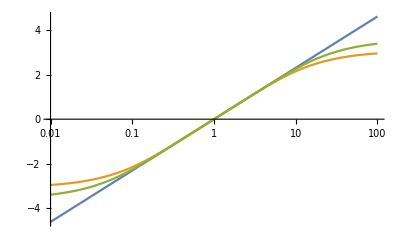

```mathematica
LogLinearPlot[{Log[x],LogApprox[x,3],LogApprox[x,5]},{x,0.01,100}]
```

#### L' erreur croît comme l’amplitude du domaine de calcul. On se propose donc de limiter le range à une octave centrée sur l’unité. L’expérimentation ci-dessous montre qu’en restreignant le calcul à ce range d’une octave, un développement limité à l’ordre 5 limite l’erreur à une valeur inférieure à la précision d’un flottant simple précision.

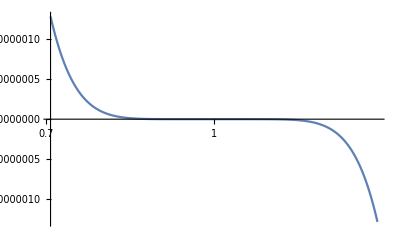

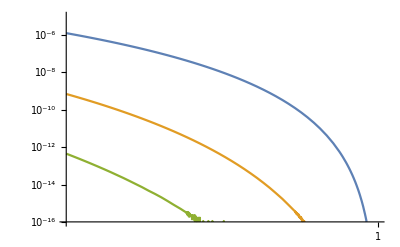

```mathematica
LogLinearPlot[LogApprox[x,3]-Log[x],{x,1/(√2),√2},PlotRange->All]
LogLogPlot[{LogApprox[x,3]-Log[x],LogApprox[x,5]-Log[x],LogApprox[x,7]-Log[x]},{x,1/(√2),1},PlotRange->{10^-16,10^-5}]
```